## Ejemplo 1

```mathematica
Abs[(Sin[0.5]+Log[E^2])/(Cos[1.2]-Sqrt[23])]
```

0.559251

## Otros

```mathematica
N[Cos[3],30](*30 es el número de decimales que quiere que te de*)
```

-0.989992496600445457271572794731

```mathematica
?N
```

### Símbolos

-Graphics-

-Graphics-

-Graphics-

#### Formas de calcular

```mathematica
Sin[Sqrt[8.]]
```

0.308072

```mathematica
8.//Sqrt//Sin (*Hace el órden inverso, de derecha  a izquierda*)
```

0.308072

#### Simplificar

```mathematica
(a^2-2a b+b^2)/(a^2-b^2)//Simplify(*Cuando se quieren multiplicar dos letras tienen que escribirse separadas a b != ab*)
```

(a-b)/(a+b)

#### Expandir

```mathematica
Expand[(a-b)^3](*Factor[]para factorizar otra vez*)
```

a^3-3 a^2 b+3 a b^2-b^3

## Variables

```mathematica
x=2;y=3;z=7;
```

```mathematica
total=x+y+z
```

12

```mathematica
y=4;
```

```mathematica
total1:=x+y+z
```

```mathematica
total1
```

13

#### Borrado de variables

```mathematica
Clear["Global`*"]
```

```mathematica
x (*Se elimina el valor de todas las variables*)
```

x

#### Sustitución de variables

```mathematica
t*(x-1)^2/.x->2
```

t

```mathematica
t*(x-1)^2/.{t->2,x->5}
```

32

## Listas

```mathematica
l1={1,2,3,4,5,6};
```

```mathematica
Length[l1](*Cuántos elementos tiene la lista*)
```

6

```mathematica
l1[[4]]^2-l1[[2]](*Doble corchete y número para ver el valor que ocupa ese lugar*)
```

14

```mathematica
l2=Range[1,100,3](*[Min,Max,Salto]*)
```

{1,4,7,10,13,16,19,22,25,28,31,34,37,40,43,46,49,52,55,58,61,64,67,70,73,76,79,82,85,88,91,94,97,100}

```mathematica
l3=Table[a^2+Log[3,2a+1.],{a,10,20,5}]
```

{102.771,228.126,403.38}

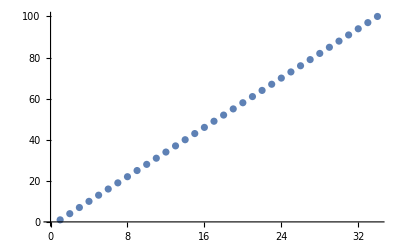

```mathematica
ListPlot[l2](*Representación*)
```

## Funciones

```mathematica
f[x_]:=Sin[x]
```

```mathematica
g[x_]:=f'[x]
```

```mathematica
h[x_]:=2f[x]
```

```mathematica
N[f[1],3]
```

0.841

### Representación de funciones

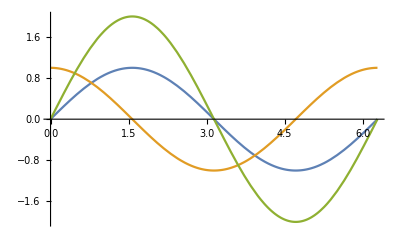

```mathematica
Plot[{f[x],g[x],h[x]},{x,0,2Pi}]
```

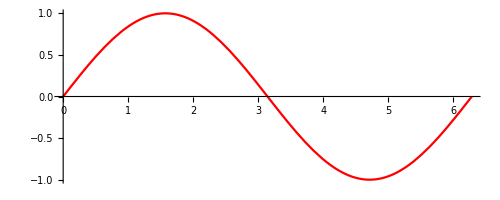

```mathematica
Plot[{f[x]},{x,0,2Pi},PlotStyle->Red,AspectRatio->Automatic]
```

```mathematica
Clear["Global`*"]
```

#### En el plano

```mathematica
f[x_,y_]:=Sin[x]*Cos[y]
```

```mathematica
Plot3D[f[x,y],{x,0,6Pi},{y,0,6Pi},PlotStyle->Red]
```

-Graphics3D-